## Double Pendulum

## Completed and Analyzed in class, February 25, 2025

This is the tenth notebook for you to complete.

### Double Pendulum — Angular Accelerations — Recap

Copied over from the theory we just presented (without derivation):

α_1=(1/16 ω_2^2 sin(θ_2-θ_1)-4 π^2 sinθ_1+1/16 ω_1^2 sin(θ_2-θ_1)cos(θ_2-θ_1)+π^2 sinθ_2 cos(θ_2-θ_1))/(1-1/4 cos^2(θ_2-θ_1))

α_2=-4 α_1 cos(θ_2-θ_1)-4 ω_1^2 sin(θ_2-θ_1)-16 π^2 sinθ_2

Well, that is a bit messy to code up, but we can do it:

```mathematica
alpha1[theta1_,theta2_,omega1_,omega2_]:=(1/16 omega2^2 Sin[theta2-theta1]-4 Pi^2 Sin[theta1]+1/16 omega1^2 Sin[theta2-theta1]Cos[theta2-theta1]+Pi^2 Sin[theta2]Cos[theta2-theta1])/(1-1/4 Cos[theta2-theta1]^2)

alpha2[theta1_,theta2_,omega1_,omega2_]:=-4alpha1[theta1,omega1,theta2,omega2]Cos[theta2-theta1]-4 omega1^2 Sin[theta2-theta1]-16 Pi^2 Sin[theta2];
```

### Initial Conditions

First set up the duration. Let’s also define steps and deltaT while we are at it:

```mathematica
tInitial = 0.0;
tFinal = 20.0;
steps = 60000;
deltaT = (tFinal - tInitial)/steps;
```

We’ll pull longer pendulum back to -45° and the shorter one we’ll just let hang straight down:

```mathematica
theta1Initial=-90°;
theta2Initial=90°;
omega1Initial=0.0;
omega2Initial=0.0;
```

```mathematica
initialConditions={tInitial,theta1Initial,theta2Initial,omega1Initial,omega2Initial}
```

{0.,-90 °,90 °,0.,0.}

### Second-Order Runge-Kutta — Double Pendulum — Recap

Also copied over from the theory:

t_(i+1)=t_i+Δt

θ_1^*=θ_1(t_i)+ω_1(t_i)·Δt/2

θ_2^*=θ_2(t_i)+ω_2(t_i)·Δt/2

ω_1^*=ω_1(t_i)+α_1(θ_1,ω_1,θ_2,ω_2)·Δt/2

ω_2^*=ω_2(t_i)+α_2(θ_1,ω_1,θ_2,ω_2)·Δt/2

ω_1(t_(i+1))=ω_1(t_i)+α_1(θ_1^*,ω_1^*,θ_2^*,ω_2^*)·Δt

ω_2(t_(i+1))=ω_2(t_i)+α_2(θ_1^*,ω_1^*,θ_2^*,ω_2^*)·Δt

θ_1(t_(i+1))=θ_1(t_i)+ (ω_1(t_i)+ω_1(t_(i+1)))Δt/2

θ_2(t_(i+1))=θ_2(t_i)+ (ω_2(t_i)+ω_2(t_(i+1)))Δt/2

### Second-Order Runge-Kutta — Implementation

```mathematica
rungeKutta2[cc_]:=(
curTime=cc[[1]];
curTheta1=cc[[2]];
curTheta2=cc[[3]];
curOmega1=cc[[4]];
curOmega2=cc[[5]];
newTime=curTime+deltaT;
theta1Star=curTheta1+curOmega1 deltaT/2;
theta2Star=curTheta2+curOmega2 deltaT/2;
omega1Star=curOmega1+alpha1[curTheta1,curTheta2,curOmega1,curOmega2] deltaT/2;
omega2Star=curOmega2+alpha2[curTheta1,curTheta2,curOmega1,curOmega2] deltaT/2;
newOmega1=curOmega1+alpha1[theta1Star,theta2Star,omega1Star,omega2Star]deltaT;
newOmega2=curOmega2+alpha2[theta1Star,theta2Star,omega1Star,omega2Star]deltaT;
newTheta1=curTheta1+(curOmega1+newOmega1)deltaT/2;
newTheta2=curTheta2+(curOmega2+newOmega2)deltaT/2;
{newTime,newTheta1,newTheta2,newOmega1,newOmega2}
)
rungeKutta2[initialConditions]
```

{0.000333333,-1.57079,1.5708,0.0131595,-1.35288×10^-6}

#### Using NestList[] to Repeatedly Apply rungeKutta2[]

```mathematica
rk2Results=Transpose[NestList[rungeKutta2,initialConditions,steps]];
```

#### Transposing to Get Points We Can Put in ListLinePlot[]

```mathematica
times=rk2Results[[1]];
theta1s=rk2Results[[2]];
theta2s=rk2Results[[3]];
```

```mathematica
times
```

```mathematica
timesAndTheta1s=Transpose[{times,theta1s}];
timesAndTheta2s=Transpose[{times,theta2s}];
```

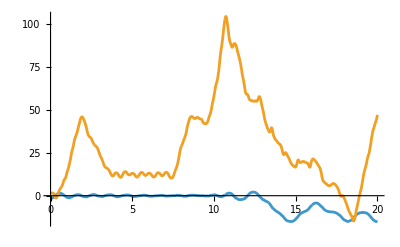

```mathematica
ListLinePlot[{timesAndTheta1s,timesAndTheta2s}]
```

#### A Graphic

The graphics work is straightforward but a little time-consuming, and not terribly instructive, so it is already all done:

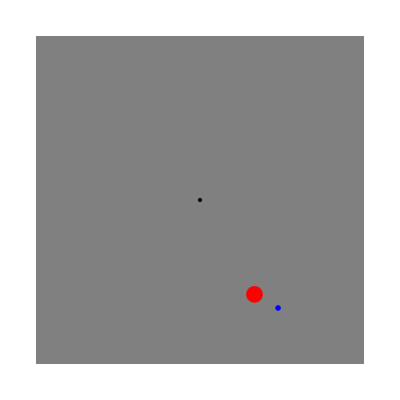

```mathematica
doublePendulumGraphic[{theta1_,theta2_}]:=Graphics[{
halfWidth=6;
buffer=0.5;
center={0.0,0.0};
mass1Point=4{Sin[theta1],-Cos[theta1]};
mass2Offset={Sin[theta2],-Cos[theta2]};
mass2Point=mass1Point+mass2Offset;
(* the next line makes a gray square *)
{EdgeForm[Thin],Gray,Polygon[{{-halfWidth,-halfWidth},{-halfWidth,halfWidth},{halfWidth,halfWidth},{halfWidth,-halfWidth}}]},
(* the next two lines make the rods that hold the masses *)
(* finally we draw the center and the masses *)
Point[center],
Style[Point[mass1Point],PointSize[0.03],Red],
Style[Point[mass2Point],PointSize[0.01],Blue]
}]
(* A little test to see if our code at least draws equally-spaced points when the positions are all zero: *)
doublePendulumGraphic[{30°,60°}]
```

#### Animating The Graphics

```mathematica
theta1sAndtheta2s=Transpose[{theta1s,theta2s}]
Animate[doublePendulumGraphic[theta1sAndtheta2s[[i]]],{i,1,steps,1},DefaultDuration->3(tFinal-tInitial)]
```

#### Comparing with YouTube

Check out Goofer King’s video of the crazy, chaotic double pendulum, https://youtu.be/6nhzrq4ALMc.